# M5: Hooke’s Law and the Simple Harmonic Oscillator

## Priyanka Makin Maya Fabrikant 11/10/2016

## Introduction

In this lab we used a spring with variable weights hanging from it to explore Hooke’s Law and simple harmonic oscillators. An oscillating spring exhibits simple harmonic motion. We started with measuring the length of the stretched out spring with weights of different masses hanging from it to dermine the spring constant k. Then, with masses of 100, 200, and 300g, we tried to measure and calculate the average period of one oscillation of the spring.

## Part 1: Measurement of the Spring Constant k

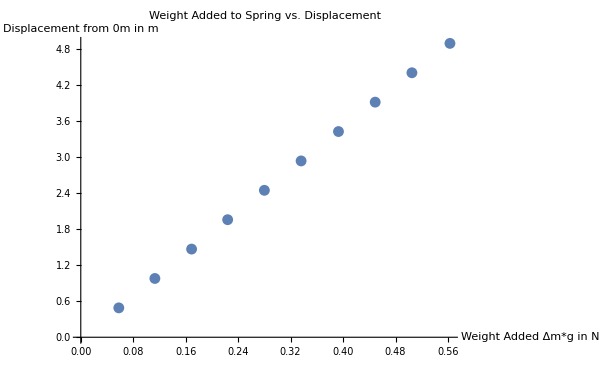

```mathematica
mspring = 0.1604; (*Mass of Spring in kg*)
δmspring = 0.0001; (*Uncertainty in the Spring's mass in kg*)

m = {0.050, 0.1, 0.15, 0.2, 0.25, 0.3, 0.35, 0.4, 0.45, 0.5}; (*Added mass in kg*)
d = {0.392, 0.447, 0.503, 0.558, 0.614, 0.67, 0.727, 0.783, 0.839, .897}; (*Measured displacement in m*)

dact = d - 0.334; (*Displacement from 0 m in m*)
weight = m*9.786; (*Weight added to spring in N*)

weightdata = Thread[{dact, weight}];
ListPlot[weightdata, PlotLabel->"Weight Added to Spring vs. Displacement", AxesLabel->{"Weight Added Δm*g in N", "Displacement from 0m in m"}]
```

I think the quality of my data is quite good because as we can see from the graph, and even if we look close at the numerical data, the data is really near linear. This means that the weight added to the spring directly correlates to the displacement of the spring from 0m. 
In the code below, I think that the Length[] function represents the number of elements of whatever you pass into it.

```mathematica
kdata = weight/dact (*List of k Values*)
kavg = (∑_(i=1)^Length[kdata] kdata[[i]])/Length[kdata] (*Average Value of k in N/m*)
ksd = √((∑_(i=1)^Length[kdata] (kdata[[i]] - kavg)^2)/(Length[kdata] - 1)); (*Standard Deviation of k in N/m*)
ksdom = ksd/√Length[kdata](*Standard of the mean of k in N/m*)
```

{8.43621,8.66018,8.6858,8.7375,8.7375,8.7375,8.71527,8.71804,8.7202,8.69094}

8.68391

0.0286848

So, the best value for k is (8.68 ± 0.03) N/m. I think that this value must be reasonable because in the part above, I determined that that data was relatively accurate. This means kdata = weight/dact must also be pretty accurate because both the weight and dact were determined from already accurate data.

## Part 2: Measurement of the Period

```mathematica
m2 = {0.1, 0.2, 0.5}; (*Hooked Masses mass in kg*)
Tavg = {0.8012, 1.0516, 1.2528}; (*Average period of 50 oscillations in s*)

meff = m2 + (0.281*mspring); (*Effective mass in kg*)

Tcalc = 2π √(meff/kavg)(*Calculated period in s*)

δTcalc = Tcalc[[1]] √((1/2*0.0001/meff[[1]])^2+(1/2*ksdom/kavg)^2)(*Uncertainty on T for the first point in s*)
```

{0.812109,1.05553,1.57416}

0.00137018

For the 100g mass, the calculated period is (0.812 ± 0.001) s.

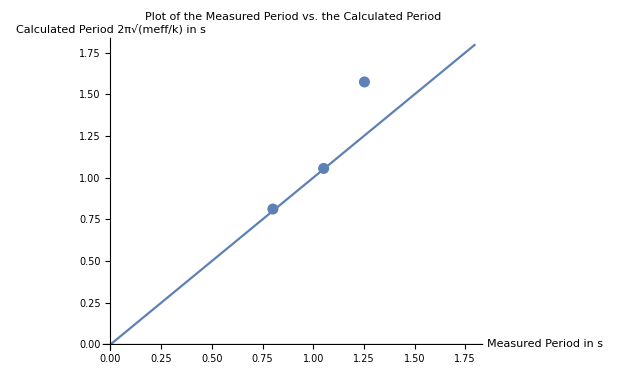

{0.986567,0.99628,0.795852}

```mathematica
Tdata = Thread[{Tavg, Tcalc}];
Tplot = Show[Plot[x, {x, 0, 1.8}], ListPlot[Tdata], PlotLabel->"Plot of the Measured Period vs. the Calculated Period", AxesLabel->{"Measured Period in s", "Calculated Period 2π√(meff/k) in s"}]
Rvalue = Tavg/Tcalc
```

For the 100 and 200g weights, the measured period lines up pretty well with the calculated period. However, for the 300g weight, we can see that the measured weight does not agree with the calculated one because that point does not lie on the line of best fit. This just goes to show that the Rvalue of precise data should be 1. If we look at the above Rvalues, the 100 and 200g Rvalues are quite close to 1, but the Rvalue for the 300g weight is the farthest from 1.

## Conclusion

I feel as though I was quite successful in this lab. For Part 1, I think I gathered the most accurate data out of all the labs so far. I determined from my data that the weight added to the spring is linearly dependent to its displacement. In Part 2, I wasn’t quite successful but still did pretty well. From my data, I decided that the measured periods for the 100 and 200g weight were quite accurate and that the 300g weight was the only one that was a little off the expected calculated value. This may have occured for a number of reasons, one being that I didn’t time the period correctly. The error could have also arisen from miscounting how many oscillations had occured.